## Initialization

### Import dependencies

```mathematica
(* Run bubble-4a-murphree.nb before. *)
```

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}
```

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

```mathematica
If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

```mathematica
Get["MovingTrap-murphree.m"]
Get["FitCurveHacked-mean-murphree.m"]
```

The following variables used by ExpansionPlotHacked are protected by this package: {axis, trap, usemodel, frequency, trapposition, gridlines, size, meanfrequency, meanmodel}

### Define initial and final trap parameters

These values taken from SM3 “predictions”

```mathematica
(** Current to field magnitude conversion factors for Bias **)
BxCalib=40.625;(*[G/A]*)
ByCalib=14.286;(*[G/A]*)
BzCalib=-10.368;(*[G/A]*)

(** Max current values **)
(* Chip *)
IlbMax=3.5; (* [A] *)
IzbMax=-3.5;(* [A] *)
IhMax=5.;(* [A] *)

(* Bias coils *)
IbxMax=8.;(*[A]*)
IbyMax=3.02;(*[A]*)
IbzMax=3.;(*[A]*)

(** Table values **)
(* These were taken from CAL3A_chiptrap_v1.pdf *)
(* Initial trap *)
tableZLHb={
(* Chip *)
AZ1=0.243,(* % *)
AZ2=-0.686,(* % *)
H1pH2=0.46,(* % *) 

(* Bias coils *)
T1=0.0275,(*%*)
T2=T1,
Y=0.85,(*%*)
Z=-0.05(*%*)
};

fdec=0.2;
tableZLHbDecomp={
(* Chip *)
tableZLHb⟦1⟧, (* AZ1 [%] *)
tableZLHb⟦2⟧,(* AZ2 [%] *)
tableZLHb⟦3⟧,(* H1pH2 [%] *)

(* Bias coils *)
fdec*tableZLHb⟦4⟧,(* T1 [%] *)
fdec*tableZLHb⟦5⟧,(* T2 [%] *)
fdec*tableZLHb⟦6⟧,(* Y [%] *)
fdec*tableZLHb⟦7⟧(* Z [%] *)
};

tableZHb={
(* Chip *)
0., (* AZ1 [%] *)
-0.743, (* AZ2 [%] *)
0.46, (* H1pH2 [%] *)

(* Bias coils *)
-0.018, (* T1 [%] *)
-0.018, (* T2 [%] *)
0.63,(* Y [%] *)
-0.0001 (* Z [%] *)
};

tableZHbC={
(* Chip *)
0., (* AZ1 [%] *)
0.914, (* AZ2 [%] *)
0.26, (* H1pH2 [%] *)

(* Bias coils *)
-0.006125,(* T1 [%] *)
-0.006125,(* T2 [%] *)
0.0677, (* Y [%] *)
-0.11367 (* Z [%] *)
};

(* Trap CurrL, CurrZ, CurrH, Bx1, By1, Bz1 *)
defineTableFromTrap[trap_]:=Module[
{CurrL=trap⟦1⟧,
CurrZ=trap⟦2⟧,
CurrH=trap⟦3⟧,
Bx1=trap⟦4⟧,
By1=trap⟦5⟧,
Bz1=trap⟦6⟧,
table},

table={
CurrL/IlbMax, (*AZ1 [%]*)
CurrZ/IzbMax, (*AZ2 [%]*)
CurrH/IhMax, (*H1pH2 [%]*)

Bx1/(-1.*IbxMax*BxCalib), (*T1*)
Bx1/(-1.*IbxMax*BxCalib), (*T2*)
By1/(IbyMax*ByCalib), (*Y*)
Bz1/(IbzMax*BzCalib) (*Z*)
};
Return[table];
];

defineTrapFromTable[table_]:=Module[
{AZ1=table⟦1⟧,
AZ2=table⟦2⟧,
H1pH2=table⟦3⟧,
T1=table⟦4⟧,
T2=table⟦5⟧, (* Currently T2=T1, and so doesn't play role yet *)
Y=table⟦6⟧,
Z=table⟦7⟧,
trap},

trap={
(* Chip *)
AZ1*IlbMax,(*Ilb0 [A]*)
AZ2*IzbMax,(*Izb0 [A]*)
H1pH2*IhMax,(*Ih0 [A]*)

(* Bias coils *)
(-1.)*T1*IbxMax*BxCalib,(*Bx [G]*)
Y*IbyMax*ByCalib,(*By [G]*)
Z*IbzMax *BzCalib(*Bz [G]*)
};
Return[trap];
]

(* The Bates trap *)
currLa=0;
currZa=0;
currLb=0;
currZb=2.6;
currH = 2.6;

Bx1 = (-0.048)*40.625;
By1 = (0.43)*14.286;
Bz1 = (0.3003)*(-10.3675);

trapZHbB={currLa,currZa,currLb,currZb,currH,Bx1,By1,Bz1};
tableZHbB=convertTrapParametersToCALTable[trapZHbB,verbose->True];
(* *)

(* Package for resale: *)
(* Compare these values to those in SM3 "predictions", although Bzfinal, for us, should be multiplied by 0.2 *)
trapzero=defineTrapFromTable[tableZLHb]
trapone=trapZHbB⟦3;;⟧
(* Where the x turn happens. *)
trapone={0.11975890500000008,2.57197881,2.557757,-2.933909875000001,10.441794117420002,-2.4559802811975002}
(*trapone=trapzero⟦1;;3⟧~Join~trapone⟦4;;6⟧*)
(*trapone=defineTrapFromTable@defineTableFromTrap@{CurrL,CurrZ,CurrH,Bx1,By1,Bz1}*)
trapzero={0.11975890500000008,2.57197881,2.557757,-2.933909875000001,10.441794117420002,-2.4559802811975002}
trapone=trapZHbB⟦3;;7⟧~Join~{-3.1134}
```

AZ1_sel | AZ2_sel | AZ1 | AZ2 | H1&H2 | T1 | T2 | Y | Z
0 | 0 | 0. | -0.742857 | 0.52 | 0.006 | 0.006 | 0.142384 | 0.100095

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0,2.6,2.6,-1.95,6.14298,-3.11336}

{0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}

{0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}

{0,2.6,2.6,-1.95,6.14298,-3.1134}

### Define target ramp analytic function

```mathematica
cass[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2 t^(1/4) -1)]/Tanh[5];
cassShort[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2(t/2)^(1/4) -1)]/Tanh[5];
```

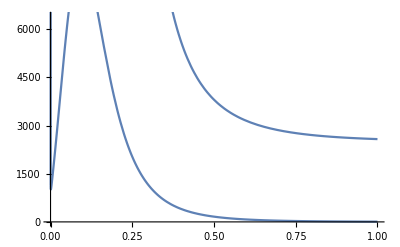

```mathematica
omegaPlot=Plot[cassShort[800,50,t]^2,{t,0,1},PlotRange->All];
dOmegaPlot=Plot[Evaluate[(1/0.5)*Abs@D[cassShort[800,50,t],t]],{t,0,1},PlotRange->All,PlotStyle->{"Red"}];
Show[omegaPlot,dOmegaPlot,PlotRange->{{0,1},{0,6400}}]
```

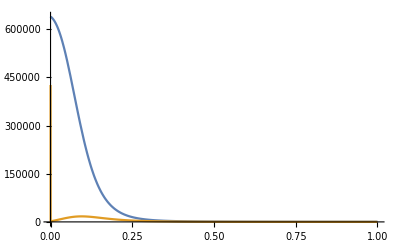

```mathematica
periodT=0.250 (* [s] *);
omegaI=800 (* [Hz] *);
omegaF=20 (* [Hz] *);
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->All,PlotStyle->{"Blue","Red"}]
```

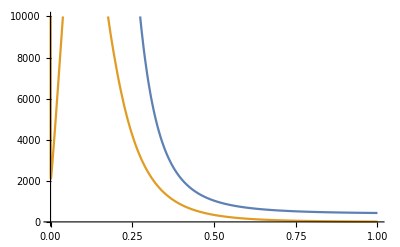

```mathematica
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->{{0,1},{0,1*10^4}},PlotStyle->{"Blue","Red"}]
```

21

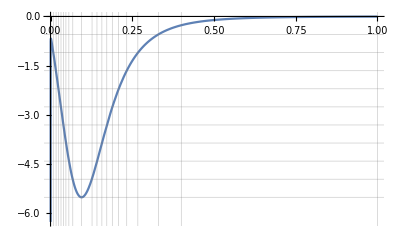

```mathematica
num=20;
times={0,0.0085,0.017,0.024,0.032,0.04,0.047,0.056,0.068,0.095,0.127,0.142,0.157,0.172,0.189,0.208,0.233,0.267,0.33,0.4,1};
Length@times
Plot[Evaluate[D[cassShort[1,0,t],{t,1}]],{t,0,1},GridLines->{times,Table[-k*max/(num/2),{k,1,num/2}]}]
```

```mathematica
Length@Differences@times
```

20

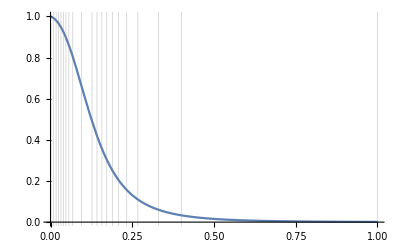

```mathematica
Plot[cassShort[1,0,t],{t,0,1},GridLines->{times,{}},PlotRange->Full]
```

```mathematica
max=MaxValue[{Abs@Evaluate[D[cassShort[1,0,t],{t,1}]],t>0.01},t]
```

5.51458

```mathematica
dCassShort[t_]=Evaluate[D[cassShort[1,0,t],{t,1}]];
```

```mathematica
(*InverseFunction@dCassShort*)
```

```mathematica
(*cassShortInv=InverseFunction@dCassShort*)
```

```mathematica
(*cassShortInv[-max]*)
```

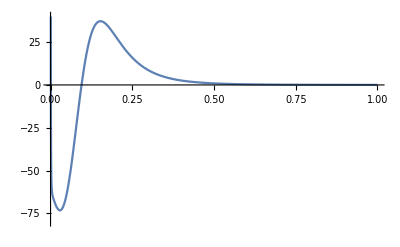

```mathematica
Plot[Evaluate[D[cassShort[1,0,t],{t,2}]],{t,0,1},PlotRange->{{0,1},{-80,40}}]
```

```mathematica
corgierSimp[t_]:=Module[{tau=2*Pi*t},
(1/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];
```

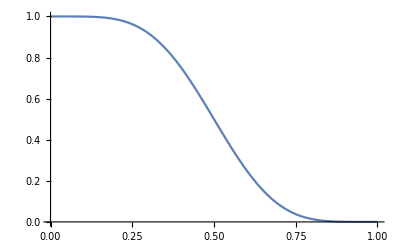

```mathematica
Plot[1-corgierSimp[t],{t,0,1}]
```

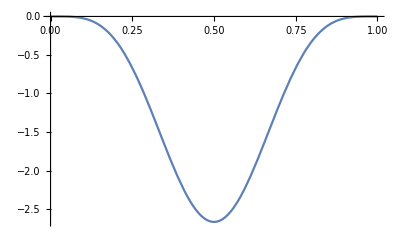

```mathematica
Plot[Evaluate@D[1-corgierSimp[t],t],{t,0,1}]
```

```mathematica
InverseFunction[corgierSimp][8/3]
```

Root2.56Root[{-32-(8 Sin[2 π #1])/π+Sin[4 π #1]/π+12 #1&,2.56420663113429131513147635321}]2.5642066311342915

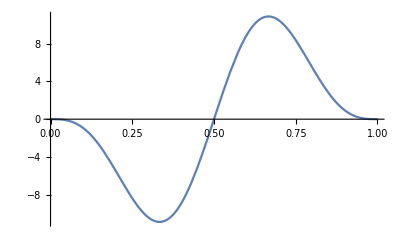

```mathematica
Plot[Evaluate@D[1-corgierSimp[t],{t,2}],{t,0,1}]
```

```mathematica
ArcCos[-1-2*Sqrt[2*6/10]]/(2*Pi)//N
```

0.5-0.290925 ⅈ

```mathematica
trapAnalytic[trap1_,trap2_,t_]:=trap1+(trap2-trap1)*(1-cassShort[1,0,t]);
zeroCrossing[trap1_,trap2_]:=(1/8)*((1/5)*ArcTanh[2*Tanh[5]*((1/2)-trap2[[6]]/(trap2[[6]]-trap1[[6]]))]+1)^4;
```

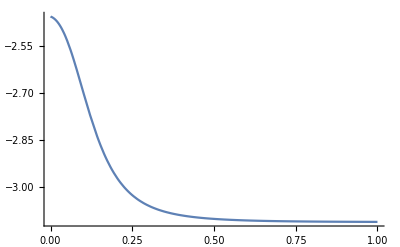

0.0442205+0.131029 ⅈ

tZero = 0.0221103 + 0.0655145 I

```mathematica
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All]
tauZero=zeroCrossing[trapzero,trapone]
period=500*10^(-3);
deltaTau=10*^-3/period;
newTaus={tauZero-deltaTau,tauZero,tauZero+deltaTau};
Print["tZero = "<>ToString[tauZero*period]]
```

```mathematica
Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,rampin1sguess⟦1⟧}]
```

{{0.02,-2.4722},{0.02,-2.4722},{0.02,-2.4722},{0.02,-2.4722},{0.02,-2.4722},{0.02,-2.4722},{0.03,-2.48711},{0.03,-2.48711},{0.03,-2.48711},{0.03,-2.48711},{0.03,-2.48711},{0.03,-2.48711},{0.03,-2.48711},{0.03,-2.48711},{0.03,-2.48711},{0.05,-2.53112},{0.08,-2.62566},{0.14,-2.8316},{0.16,-2.88593},{0.18,-2.93066}}

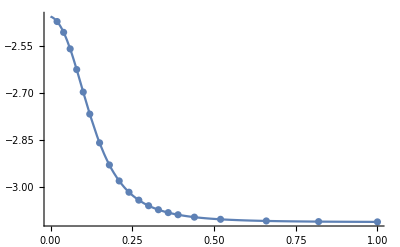

```mathematica
Show[{
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All],
ListPlot[Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,Accumulate@rampin1sguess⟦1⟧}]]
}]
```

### Define ramp ansatz

#### Trap 1 Short

```mathematica
rampin1sguess={{0.02,0.02,0.02,0.014,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.036,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.014,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.036,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
rampin1sguess={2*{0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.025,0.04,0.07,0.08,0.09},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
(*(* New as of 4 September 2020---an attempt to divy up the ramp based on its slope *)
Total@Differences@times
rampin1sguess={Differences@times,{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}*)
```

```mathematica
Table[Total@#[[1,1;;m]],{m,Length@#[[1]]}]&[rampin1sguess]
```

{0.02,0.04,0.06,0.08,0.1,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.44,0.52,0.66,0.82,1.}

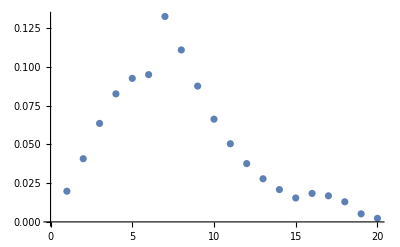

```mathematica
ListPlot[rampin1sguess⟦2⟧]
```

```mathematica
(*rampin1sguess⟦1,9;;13⟧
rampin1sguess⟦1⟧=Join[rampin1sguess⟦1,1;;9⟧,{0.01,0.01,0.01,0.01,0.01},rampin1sguess⟦1,10;;⟧]
rampin1sguess⟦1,9;;18⟧
rampin1sguess⟦1,9;;18⟧={0.02,0.02,0.02,0.01,0.01,0.01,0.01,0.01,0.02,0.02}*)
```

```mathematica
(*rampin1sguess⟦2,9;;13⟧
rampin1sguess⟦2⟧=Join[rampin1sguess⟦2,1;;9⟧,ConstantArray[0.,5],rampin1sguess⟦2,10;;⟧]*)
```

```mathematica
(*rampin1sguess*)
```

```mathematica
Total[rampin1sguess⟦1⟧]
```

1.

```mathematica
Total[rampin1sguess⟦2⟧]
```

1.

```mathematica
Length@rampin1sguess[[1]]
```

20

## Calculate ramp

The following took 8 1/2 minutes to complete. (1 1/4 hr on the Dell)

```mathematica
(* 
If FitCurveHacked runs in less than a second and has multiple errors citing GeometricMean, go back and make sure bubble-4a.nb was run before this notebook. MovingTrap-murphree.m calls ChipTrapFrequencies, which is defined in that notebook.
*)
```

```mathematica
(rampin1s=FitCurveHacked[trapzero,trapone,rampin1sguess,nramps1short,-3.5,-5])//Timing
```

{0.50991,-17.7534,0.00001}

Completed point 1 of 19 in 43.875 s (Total time: 0.73125 min).

{0.50947,-16.6589,0.00001}

{0.04617,0.0329727,0.00001}

{0.04708,-0.0019715,0.00001}

Completed point 2 of 19 in 50.5469 s (Total time: 1.5737 min).

{0.49715,-15.0605,0.00001}

{0.07329,-0.0216624,0.00001}

Completed point 3 of 19 in 41.7031 s (Total time: 2.26875 min).

{0.46975,-13.1167,0.00001}

{0.09069,0.0767553,0.00001}

{0.0922,0.0213834,0.00001}

{0.09296,-0.00647713,0.00001}

Completed point 4 of 19 in 50.4375 s (Total time: 3.10938 min).

{0.42791,-11.0157,0.00001}

{0.10668,-0.0853308,0.00001}

Completed point 5 of 19 in 43.0781 s (Total time: 3.82734 min).

{0.37665,-9.02568,0.00001}

{0.10572,-0.0102262,0.00001}

Completed point 6 of 19 in 37.625 s (Total time: 4.45443 min).

{0.34205,-6.45151,0.00001}

Completed point 7 of 19 in 26.9531 s (Total time: 4.90365 min).

{0.25957,-4.59566,0.00001}

{0.11338,-0.00592234,0.00001}

Completed point 8 of 19 in 35.4688 s (Total time: 5.49479 min).

{0.19087,-3.27372,0.00001}

{0.08472,-0.0108164,0.00001}

Completed point 9 of 19 in 47.2344 s (Total time: 6.28203 min).

Completed point 10 of 19 in 4. s (Total time: 6.3487 min).

{0.0335,0.311316,0.00001}

{0.03908,0.142347,0.00001}

{0.04187,0.0579883,0.00001}

{0.04327,0.0156891,0.00001}

{0.04397,-0.00545261,0.00001}

Completed point 11 of 19 in 37.625 s (Total time: 6.97578 min).

{0.02396,0.21156,0.00001}

{0.02795,0.092194,0.00001}

{0.02995,0.032428,0.00001}

{0.03095,0.00256138,0.00001}

Completed point 12 of 19 in 33.25 s (Total time: 7.52995 min).

Completed point 13 of 19 in 4.375 s (Total time: 7.60286 min).

{0.0362,-0.57044,0.00001}

Completed point 14 of 19 in 24.2969 s (Total time: 8.00781 min).

{0.02507,-0.374325,0.00001}

{0.01254,-0.00838878,0.00001}

Completed point 15 of 19 in 27.3438 s (Total time: 8.46354 min).

{0.0198,-0.182005,0.00001}

Completed point 16 of 19 in 17.5313 s (Total time: 8.75573 min).

{0.01167,0.0209557,0.00001}

{0.01297,-0.0167066,0.00001}

Completed point 17 of 19 in 19.0313 s (Total time: 9.07292 min).

{0.00196,0.218322,0.00001}

{0.00196,0.218322,0.00001}

{0.00196,0.218322,0.00001}

«311 more identical outputs»

$Aborted

```mathematica
rampin1s⟦2⟧-rampin1sguess⟦2⟧
```

{0.00191,0.00539,0.00681,0.00526,0.00312,0.00022,-0.00341,-0.00513,-0.0049,-0.00289,-0.00239,-0.00132,-0.00076,-0.00044,0.00018,-0.00033,-0.00003,-0.00002,0.00019,-0.00146}

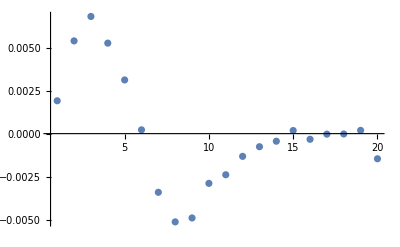

```mathematica
ListPlot[%,PlotRange->All]
```

The following took ~4 1/2 minutes to run. (~ 1 hr 12 min on Dell)

```mathematica
points1s=100;
(pts1s=MovingTrap[trapzero,trapone,rampin1s,points1s,nramps1short];)//Timing
```

{369.422,Null}

```mathematica
Position[pts1s⟦All,1,1⟧,Min@pts1s⟦All,1,1⟧]
```

{{76}}

```mathematica
pts1s⟦31⟧
```

{{0.0000165302,0.0000484525,0.000369256},{33.0841,186.687,195.123},5.99374}

```mathematica
Length@pts1s
```

101

```mathematica
trapParamVt=RampList[trapzero,trapone,rampin1s,points1s,nramps1short];
```

```mathematica
trapParamVt[[31]]
```

{0.3,{0.20538,2.55195,2.52756,-3.63735,13.5152,-1.98599}}

### Plot calculated ramp’s parameters

{{0.,1.},{4.69813,6.83513}}

{109.742,929.95}

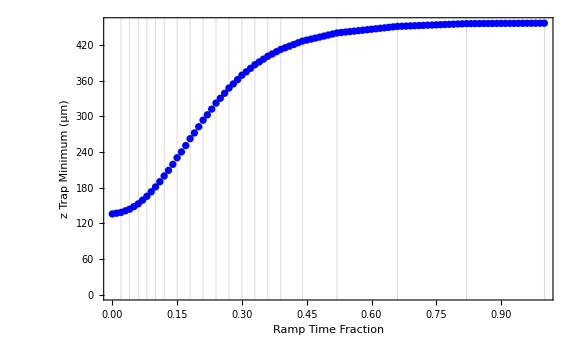
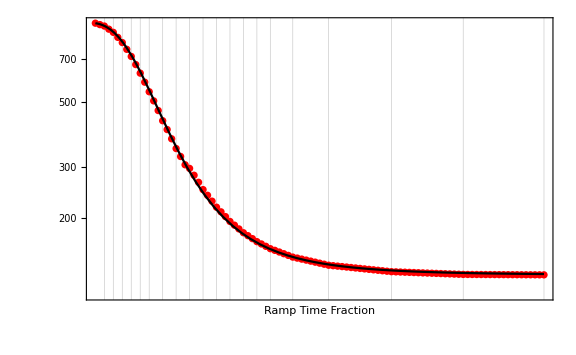

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"z"]
```

{{0.,1.},{3.19789,4.77009}}

{24.4807,117.929}

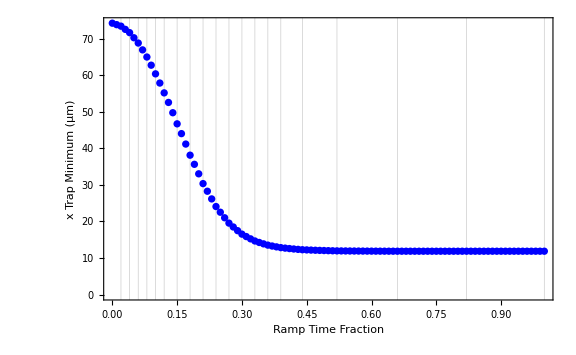
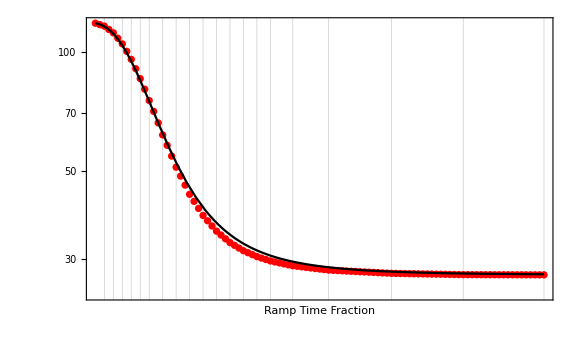

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"x",meanfrequency->False]
```

{{0.,1.},{4.6421,6.87598}}

{103.762,968.724}

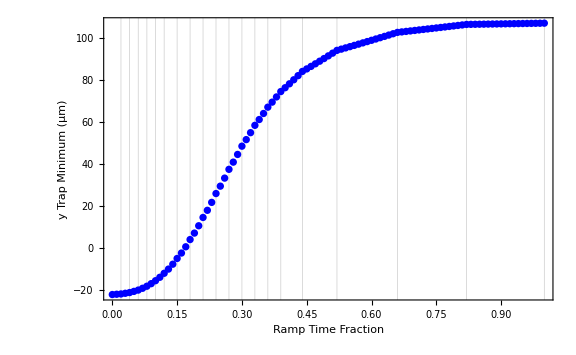
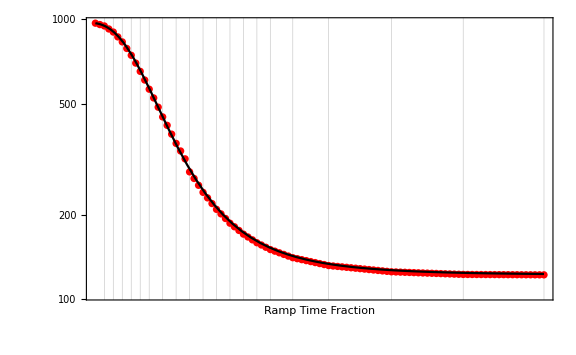

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"y",meanfrequency->False]
```

{{0.,1.},{4.69813,6.83513}}

{109.742,929.95}

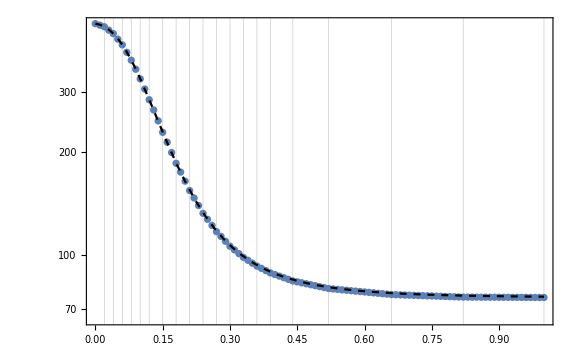

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->False,frequency->False,gridlines->True,usemodel->True,size->Large,axis->"z",meanfrequency->True,meanmodel->True]
```

```mathematica
Beep[]
```

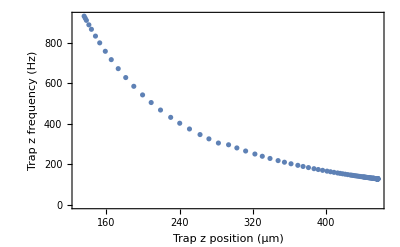

```mathematica
plotZFreqVZmin[movingtrap_]:=Module[{zs,omegas},
zs[n_]:=movingtrap⟦n,1,3⟧*10^6;
omegas[n_]:=movingtrap⟦n,2,3⟧;

ListPlot[Table[{zs[n],omegas[n]},{n,Range[Length[movingtrap]]}],Frame->True,FrameLabel->{"Trap z position (μm)","Trap z frequency (Hz)"}]
]
plotZFreqVZmin[pts1s]
```

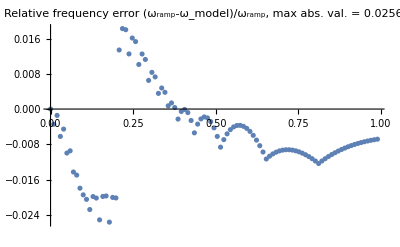

```mathematica
plotFreqError[pts1s]
```

```mathematica
printTrapParameters[{{minx_,miny_,minz_},{omegax_,omegay_,omegaz_},bmin_}]:=Print[
"Position = "<>ToString[{minx,miny,minz}*10^6]<>" μm\n"<>
"Frequency = "<>ToString[{omegax,omegay,omegaz}]<>" Hz\n"<>
"Bmin = "<>ToString[bmin]<>" G"];

printTrapParameters[pts1s⟦1⟧]
printTrapParameters[pts1s⟦-1⟧]
```

Position = {74.2507, -21.9915, 135.717} μm
Frequency = {117.929, 968.724, 929.95} Hz
Bmin = 8.97843 G

Position = {11.8576, 106.845, 456.854} μm
Frequency = {27.4397, 122.025, 128.153} Hz
Bmin = 5.60963 G

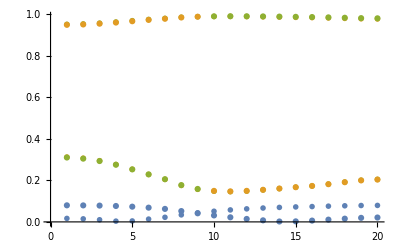

```mathematica
plotTrapPrincAxes[trap1_,trap2_,rampin_]:=Module[
{nramps=Length@rampin⟦1⟧,
eVecIndex,
characVtime,
vec2Plot,vec3Plot},
characVtime=Table[SingleTrapCharacteristics[trap1,trap2,rampin,nramps,n],{n,nramps}];
eVecIndex=2;
vec2Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}],PlotMarkers->"OpenMarkers"];
eVecIndex=3;
vec3Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}]];
Show[vec2Plot,vec3Plot]
]
plotTrapPrincAxes[trapzero,trapone,rampin1s]
```

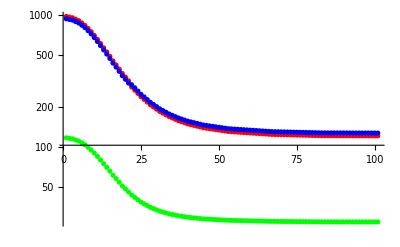

```mathematica
plotTrapYandZCharacteristics[movingramp_]:=Module[
{xFreqs=movingramp⟦All,2,1⟧,
yFreqs=movingramp⟦All,2,2⟧,
zFreqs=movingramp⟦All,2,3⟧,
xPlot,yPlot,zPlot},
xPlot=ListLogPlot[xFreqs,PlotStyle->Green];
yPlot=ListLogPlot[yFreqs,PlotStyle->Red];
zPlot=ListLogPlot[zFreqs,PlotStyle->Blue];
Show[yPlot,zPlot,xPlot,PlotRange->All]
]
plotTrapYandZCharacteristics[pts1s]
```

## Export ramp

### Export ramp

```mathematica
trap1short={#⟦1⟧,Table[Total[Take[Round[#⟦2⟧,10.^-5],n]],{n,Length@rampin1s⟦1⟧}]}&[rampin1s]
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.02173,0.0679,0.13828,0.22619,0.32195,0.41723,0.54643,0.6523,0.73506,0.79848,0.84652,0.88283,0.90991,0.93033,0.94595,0.96401,0.98082,0.99378,0.99917,1.}}

```mathematica
(* Set the DateStringFormat to help create unique names for each exported beam.The format is inspired by the ISO 8601 standard. *)
generateTimeStamp[]:=DateString[{"Year","Month","Day","T","Hour","Minute","Second"}];
rampTimeStamp=generateTimeStamp[]
```

20200904T154244

```mathematica
Export[FileNameJoin@{outputDirectory,rampTimeStamp<>"_trap1short.csv"},trap1shortᵀ]
```

C:\Users\josep\forschung\modeling\bubble_bec\output\20200904T154244_trap1short.csv

### Export ramp parameters

```mathematica
exportRampEndpoints[trap1_,trap2_,rampTimeStamp_,outputDirectory_]:=Module[
{
fileName=rampTimeStamp<>"_ramp_endpoints",
table={trap1,trap2},
headings={{"InitialTrap","FinalTrap"},{"IL[A]","IZ[A]","IH[A]","Bx[G]","By[G]","Bz[G]"}}
},
Print[table];
Export[FileNameJoin@{outputDirectory,fileName<>".csv"},table,TableHeadings->headings]
]

exportRampEndpoints[trapzero,trapone,rampTimeStamp,outputDirectory]
```

{{0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}}

C:\Users\josep\forschung\modeling\bubble_bec\output\20200904T154244_ramp_endpoints.csv

```mathematica
Beep[];
Pause[1];
Beep[];
```

```mathematica
defineTableFromTrap[trapone]
```

{0.0342168,-0.734851,0.511551,0.00902742,0.00902742,0.242024,0.0789603}

## Look at intermediate trap and CAL table values

{{0., 0.8505}, {0.01, 0.84256}, {0.02, 0.834621}, {0.03, 0.817752}, {0.04, 0.800883}, {0.05, 0.775168}, {0.06, 0.749453}, {0.07, 0.717333}, {0.08, 0.685214}, {0.09, 0.650226}, {0.1, 0.615238}, {0.11, 0.580425}, {0.12, 0.545613}, {0.13, 0.514142}, {0.14, 0.482672}, {0.15, 0.451201}, {0.16, 0.425413}, {0.17, 0.399625}, {0.18, 0.373838}, {0.19, 0.353679}, {0.2, 0.33352}, {0.21, 0.313361}, {0.22, 0.297914}, {0.23, 0.282466}, {0.24, 0.267018}, {0.25, 0.255316}, {0.26, 0.243615}, {0.27, 0.231913}, {0.28, 0.223069}, {0.29, 0.214224}, {0.3, 0.20538}, {0.31, 0.198784}, {0.32, 0.192188}, {0.33, 0.185591}, {0.34, 0.180617}, {0.35, 0.175644}, {0.36, 0.17067}, {0.37, 0.166865}, {0.38, 0.16306}, {0.39, 0.159255}, {0.4, 0.156616}, {0.41, 0.153977}, {0.42, 0.151337}, {0.43, 0.148698}, {0.44, 0.146058}, {0.45, 0.144523}, {0.46, 0.142987}, {0.47, 0.141452}, {0.48, 0.139916}, {0.49, 0.138381}, {0.5, 0.136845}, {0.51, 0.13531}, {0.52, 0.133775}, {0.53, 0.133098}, {0.54, 0.132422}, {0.55, 0.131745}, {0.56, 0.131069}, {0.57, 0.130392}, {0.58, 0.129716}, {0.59, 0.129039}, {0.6, 0.128363}, {0.61, 0.127686}, {0.62, 0.12701}, {0.63, 0.126333}, {0.64, 0.125657}, {0.65, 0.124981}, {0.66, 0.124304}, {0.67, 0.124058}, {0.68, 0.123812}, {0.69, 0.123566}, {0.7, 0.123319}, {0.71, 0.123073}, {0.72, 0.122827}, {0.73, 0.122581}, {0.74, 0.122335}, {0.75, 0.122089}, {0.76, 0.121842}, {0.77, 0.121596}, {0.78, 0.12135}, {0.79, 0.121104}, {0.8, 0.120858}, {0.81, 0.120612}, {0.82, 0.120365}, {0.83, 0.120332}, {0.84, 0.120298}, {0.85, 0.120264}, {0.86, 0.120231}, {0.87, 0.120197}, {0.88, 0.120163}, {0.89, 0.12013}, {0.9, 0.120096}, {0.91, 0.120062}, {0.92, 0.120028}, {0.93, 0.119995}, {0.94, 0.119961}, {0.95, 0.119927}, {0.96, 0.119894}, {0.97, 0.11986}, {0.98, 0.119826}, {0.99, 0.119793}, {1., 0.119759}}

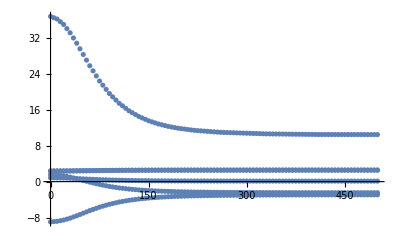

```mathematica
listRampCALTables[trap1_,trap2_,rampin_,npoints_,nramps_:3]:=Module[
{
deltatrap=trap1-trap2,
ramp=Prepend[Table[{Sum[#[[1,i]],{i,n}],Sum[#[[2,i]],{i,n}],#[[2,n]]/#[[1,n]]},{n,nramps}]&[rampin],{0,0,0}],
ramplist,
colors={"Red","Orange","Yellow","Green","Blue","Black"}
},

ramplist=Prepend[Drop[Table[{t,Piecewise[Table[{#3-(#1[[n-1,2]]+#1[[n,3]]*(t-#1[[n-1,1]]))*#2,#1[[n-1,1]]<t<=#1[[n,1]]},{n,2,nramps+1}]&[ramp,deltatrap,trap1]]},{t,0.,1.,1./npoints}],1],{0.,trap1}];

Print[ToString[{#[[1]],#[[2,1]]}&/@ramplist]];

Return[Table[ListPlot[{#⟦1⟧*500,#⟦2,k⟧}&/@ramplist,PlotStyle->colors⟦k⟧],{k,6}]];
];
test=listRampCALTables[trapzero,trapone,rampin1s,points1s,nramps1short];
Show[test,PlotRange->All]
```

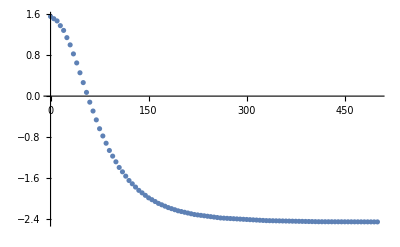

```mathematica
test[[6]]
```

```mathematica
rampin1s
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.02173,0.04617,0.07038,0.08791,0.09576,0.09528,0.1292,0.10587,0.08276,0.06342,0.04804,0.03631,0.02708,0.02042,0.01562,0.01806,0.01681,0.01296,0.00539,0.00083}}

```mathematica
plotRampCALTable[trap1_,trap2_,rampin_]:=Module[
{
deltaTrap=trap2-trap1,
totRamp=Table[{Total@rampin⟦1,1;;k⟧,Total@rampin⟦2,1;;k⟧},{k,Length@rampin⟦1⟧}]~Prepend~{0,0},
trapRamp
},
trapRamp=Table[(totRamp⟦k,2⟧*deltaTrap+trap1)~Prepend~totRamp⟦k,1⟧,{k,Length@rampin⟦1⟧+1}];
Return[trapRamp];
];
trapRamp=plotRampCALTable[trapzero,trapone,rampin1s]
trapzero
trapone
```

{{0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.02,0.834621,2.40472,2.3056,-8.80704,36.1022,1.46804},{0.04,0.800883,2.41261,2.3175,-8.52986,34.8911,1.28284},{0.06,0.749453,2.42464,2.33564,-8.10732,33.045,1.00053},{0.08,0.685214,2.43967,2.3583,-7.57955,30.7391,0.647911},{0.1,0.615238,2.45605,2.38298,-7.00464,28.2273,0.263801},{0.12,0.545613,2.47234,2.40754,-6.43262,25.7281,-0.118385},{0.15,0.451201,2.49443,2.44085,-5.65696,22.3391,-0.636629},{0.18,0.373838,2.51253,2.46813,-5.02136,19.5621,-1.06129},{0.21,0.313361,2.52668,2.48947,-4.5245,17.3913,-1.39326},{0.24,0.267018,2.53752,2.50581,-4.14375,15.7277,-1.64765},{0.27,0.231913,2.54574,2.5182,-3.85534,14.4676,-1.84034},{0.3,0.20538,2.55195,2.52756,-3.63735,13.5152,-1.98599},{0.33,0.185591,2.55658,2.53454,-3.47477,12.8049,-2.09461},{0.36,0.17067,2.56007,2.5398,-3.35218,12.2693,-2.17652},{0.39,0.159255,2.56274,2.54383,-3.2584,11.8595,-2.23918},{0.44,0.146058,2.56583,2.54848,-3.14998,11.3858,-2.31162},{0.52,0.133775,2.5687,2.55281,-3.04906,10.9449,-2.37905},{0.66,0.124304,2.57092,2.55615,-2.97125,10.6049,-2.43103},{0.82,0.120365,2.57184,2.55754,-2.93889,10.4636,-2.45265},{1.,0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}}

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}

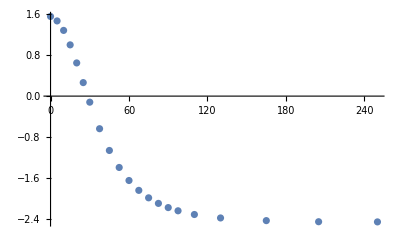

```mathematica
ListPlot[{#[[1]]*250,#[[7]]}&/@trapRamp]
```

```mathematica
Total@{1,2,3,4,5}
```

15